# Gravitational transitions via the explicitly broken symmetron screening mechanism Numerical Analysis and Construction Figures File

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];

Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol,Part::partw,NonlinearModelFit::cvmit];
```

## Figure 2 - The geometry of the spherical domain wall in the presence of spherical matter shell

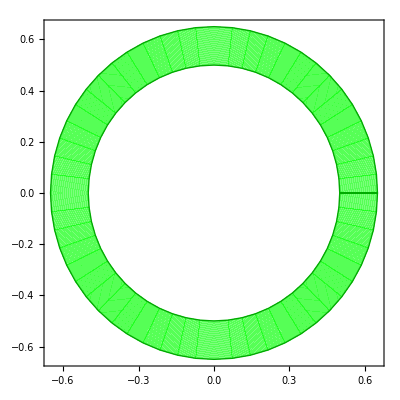

```mathematica
(*The geometry of the spherical domain wall in the presence of spherical matter shell*)
ClearAll["Global`*"] 
Clear["Global`*"]
plmat=ParametricPlot[{rr Cos[θ],rr Sin[θ]},{θ,0,2Pi},{rr,0.5,0.65},Axes->False,BoundaryStyle->Darker[Green],PlotStyle->{Green,Thick}]
```

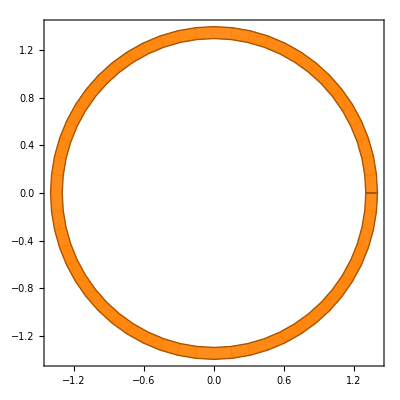

```mathematica
plwall=ParametricPlot[{rr Cos[θ],rr Sin[θ]},{θ,0,2Pi},{rr,1.3,1.4},BoundaryStyle->Darker[Orange],Axes->False,PlotStyle->{Orange,Thick}]
```

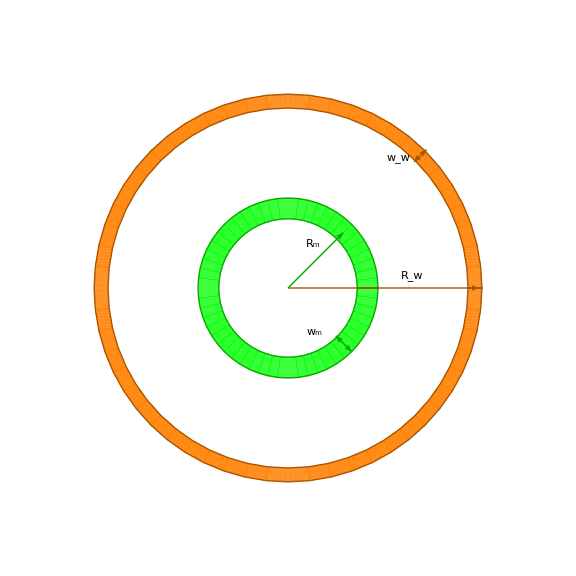

```mathematica
figshells=Show[plmat,plwall,Graphics[{Inset["R_w",{0.9,0.09},BaseStyle->{Italic,Bold,Darker[Orange],FontFamily->"Times",16}]}],Graphics[{Inset["w_w",{0.8,0.94},BaseStyle->{Italic,Bold,Darker[Orange],FontFamily->"Times",16}]}],Graphics[{Inset["R_m",{0.18,0.32},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],Graphics[{Inset["w_m",{0.19,-0.32},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],PlotRange->{{-1.7,1.7},{-1.7,1.7}},Frame ->False,BaseStyle->{Large,FontFamily->"Times",20},FrameStyle->Directive[Black,Thick],Epilog->{{Darker[Orange],Arrowheads[0.02],Arrow[{{0,0},{1.38,0}}]},{Darker[Orange],Arrowheads[{-.01,.01}],Arrow[{{0.91,0.91},{1.,1.}}]},{Darker[Green],Arrowheads[0.02],Arrow[{{0,0},{0.4,0.4}}]},{Darker[Green],Arrowheads[{-.01,.01}],Arrow[{{0.345,-0.345},{0.46,-0.46}}]},},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figshells.pdf",figshells,ImageResolution->1000];
```

## Dynamical equations and energetics of spherical asymmetron configurations

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"] 
(* rescaled effective potential of asymmetron *) 
(* V=(-1/2) (λ η^2 - ρ/Μ^2) Φ^2 + (λ/4) Φ^4 + (λ/4) η^4 + ε Φ^3 *)
(* rb=ρ/(λ η^2 M^2), phb=Φ/η, vv1=V/(λ η^4), e=ε/(λη), vv2=2vv1, m^2=λ η^2 *)

vv1=(-1/2)(1-rb)phb^2+phb^4/4+1/4+e  phb^3;
vv2=-(1-rb)phb^2+phb^4/2+1/2+2 e  phb^3;
```

```mathematica
(* find stationary points of potential(central maximum and the two local minima) *)

sol2=Solve[D[vv2,phb]==0,phb] //FullSimplify
```

{{phb→0},{phb→1/2 (-3 e-√(4+9 e^2-4 rb))},{phb→1/2 (-3 e+√(4+9 e^2-4 rb))}}

```mathematica
(* value of potential at the minima and at the central maximum *)

vvstat=vv2 /. sol2  //FullSimplify
```

{1/2,1/4 (-27 e^4-9 e^3 √(4+9 e^2-4 rb)+18 e^2 (-1+rb)+4 e √(4+9 e^2-4 rb) (-1+rb)-2 (-2+rb) rb),1/4 (-27 e^4+9 e^3 √(4+9 e^2-4 rb)+18 e^2 (-1+rb)-4 e √(4+9 e^2-4 rb) (-1+rb)-2 (-2+rb) rb)}

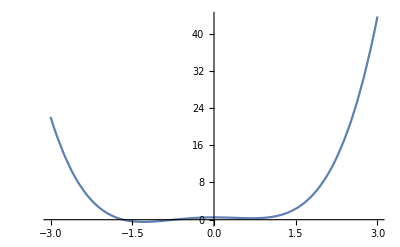

```mathematica
(* plot the potential *)

Plot[vv2/. {e->0.2,rb->0.1},{phb,-3,3}]
```

```mathematica
(* maximum of potential *)
vv0=vv2 /. phb->0
```

1/2

```mathematica
(* check the limit of e=0 *)
vvstate0=vv2 /. sol2  /. e->0 //FullSimplify
```

{1/2,-1/2 (-2+rb) rb,-1/2 (-2+rb) rb}

```mathematica
(* the width of the wall is equal to the inverse mass *)
ww=(1-rb)^(-1/2) ;
```

```mathematica
(* the value of phb at the negative phb minimum *)
phminn=sol2[[2,1,2]] ;
phminnf[rb_,e_]:=sol2[[2,1,2]] ;
```

```mathematica
(* the value of phb at the positive phb minimum *)
phminp=sol2[[3,1,2]] ;
phminpf[rb_,e_]:=sol2[[3,1,2]]  ;
```

```mathematica
(* the value of the potential at the negative phb minimum *)
vvminn=vvstat[[2]] ;
```

```mathematica
(* the value of the potential at the positive phb minimum *)
vvminp=vvstat[[3]];
```

```mathematica
(* surface density of the asymmetron wall gradiant + potential contribution *)
sigma= ((1/2)ww(phminp-phminn)/ww)^2 + vv0 ww;
```

```mathematica
(* energy of the wall induced by the surface density and the vaccua energy difference *)
enwall1= sigma R^2 + (vvminn-vvminp) R^3/3/. rb->aa R^n;
```

```mathematica
(* energy of the wall induced by the surface density and the vaccua energy difference *)
enwall2= sigma R^2 - (vvminn-vvminp) R^3/3/. rb->aa R^n;
```

## Figure 3 - I. Stable Spherical Symmetron Walls - Monotonic matter density increasing towards the center

6.59947

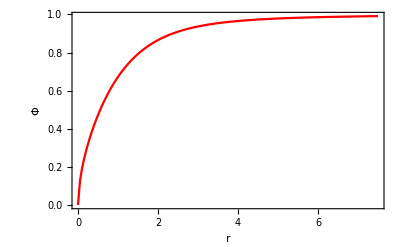

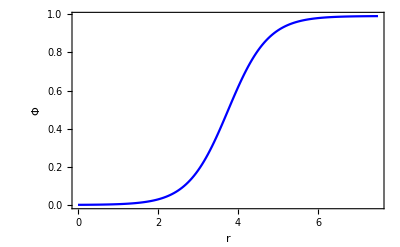

```mathematica
(* I.Stable Spherical Symmetron Walls - Monotonic matter density increasing towards the center*)

Clear[r,fp]
(* Energy Minimization (EM) method *)
r[i_]:=i dx;
fp[i_]:=(f[i]-f[i-1])/dx;
e=0; rt=1;n=-2;
ee[i_]:=r[i]^2fp[i]^2+r[i]^2(-(1-(r[i]/rt)^n)f[i]^2+f[i]^4/2+1/2+2 e  f[i]^3);
dx=0.05;
imax=150;
rmax=imax dx;
rmin=0;
rmax=r[imax];
f[0]=0;
phrmin=0;
phrmax=phminpf[rb,e] /. { rb-> (rmax/rt)^n};
f[imax]=phrmax;
etot=dx  Sum[ee[i],{i,1,imax}];
r0=rmin+(rmax-rmin)/2;
(* Initial gues *)
ft[r_]:=((phrmax-phrmin)/2) Tanh[(r-r0)]+((phrmax+phrmin)/2);
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]]
tfsol=Table[{i dx,f[i]/. sol1[[2]]},{i,0,imax}];
tstart=Table[{i dx,ft[r[i]]},{i,0,imax}];
(* final  wall configuration *)
plsmonfin=ListPlot[tfsol,Joined->True,PlotRange->All,PlotStyle->Red,Frame->True,FrameLabel->{r,Φ}]
(* initial  wall configuration *)
plsmonin=ListPlot[tstart,Joined->True,PlotRange->All,PlotStyle->Blue,Frame->True,FrameLabel->{r,Φ}]
```

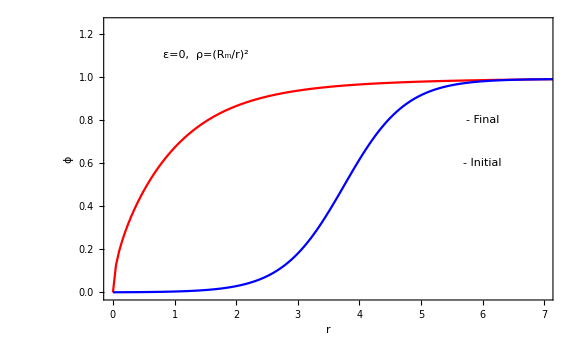

```mathematica
figsmon=Show[plsmonfin,plsmonin,Graphics[{Inset["ε=0,  ρ=(R_m/r)^2",{1.5,1.1},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],Graphics[{Inset["- Initial",{6,0.6},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",16}]}],Graphics[{Inset["- Final",{6,0.8},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],PlotRange->{{-0.01,7},{-0.01,1.25}},FrameLabel->{"r ","ϕ"},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figsmon.pdf",figsmon,ImageResolution->1000];
```

## Figure 4 - I. Stable Spherical Symmetron Walls - Increasing outward matter density

```mathematica
(* I.Stable Spherical Symmetron Walls - Increasing outward matter density *)
Clear[r,fp,ee,dx,f,rmin,rmax,r0,ftab,sol1]
```

```mathematica
(* Energy Minimization (EM) method *)
```

560.753

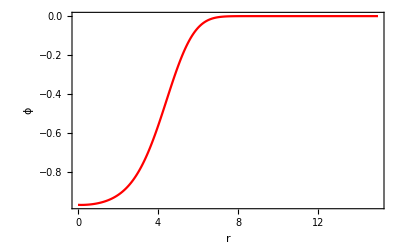

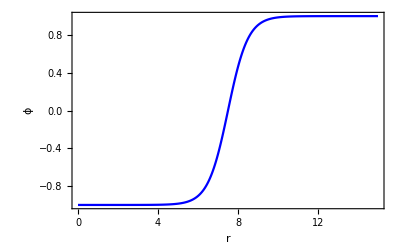

```mathematica
r[i_]:=i dx;
fp[i_]:=(f[i]-f[i-1])/dx;
e=0; rt=5;n=6;
ee[i_]:=r[i]^2fp[i]^2+r[i]^2(-(1-(r[i]/rt)^n)f[i]^2+f[i]^4/2+1/2+2 e  f[i]^3);
dx=0.05;
imax=300;
rmax=imax dx;
rmin=0;
rmax=r[imax];
f[0]=f[1];
phrmax=1;
phrmin=-1;
f[imax]=f[imax-1];
etot=dx  Sum[ee[i],{i,1,imax}];
r0=rmin+(rmax-rmin)/2;
(* Initial gues *)
ft[r_]:=((phrmax-phrmin)/2) Tanh[(r-r0)]+((phrmax+phrmin)/2);
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]]
tfsol=Table[{i dx,f[i]/. sol1[[2]]},{i,0,imax}];
tstart=Table[{i dx,ft[r[i]]},{i,0,imax}];
(* final  wall configuration *)
pls6fin=ListPlot[tfsol,Joined->True,PlotRange->All,PlotStyle->Red,Frame->True,FrameLabel->{"r","ϕ"}]
(* initial  wall configuration *)
pls6in=ListPlot[tstart,Joined->True,PlotRange->All,PlotStyle->Blue,Axes->False,Frame->True,FrameLabel->{"r","ϕ"}]
```

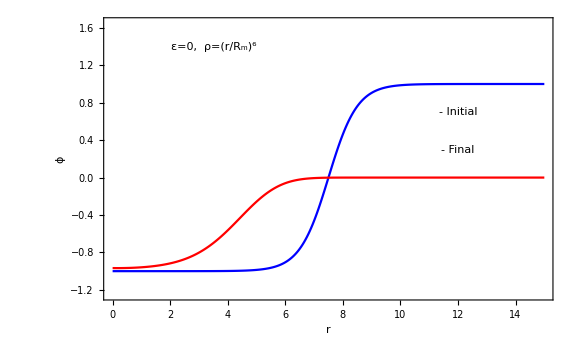

```mathematica
figs6=Show[pls6in,pls6fin,Graphics[{Inset["ε=0,  ρ=(r/R_m)^6",{3.5,1.4},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],Graphics[{Inset["- Initial",{12,0.7},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",16}]}],Graphics[{Inset["- Final",{12,0.3},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],PlotRange->{{-0.01,15},{-1.25,1.65}},FrameLabel->{"r ","ϕ"},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figs6.pdf",figs6,ImageResolution->1000];
```

## Figure 5 (middle panel) - I. Stable Spherical Symmetron Walls - Shell-like matter density

1609.01

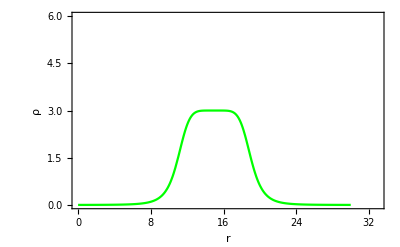

```mathematica
Clear[r,fp,ee,dx,f,rmin,rmax,r0,ftab,sol1,rrb]
(* Energy Minimization (EM) method *)
r[i_]:=i dx;
fp[i_]:=(f[i]-f[i-1])/dx;
e=0; rt=4;n=6;rm=15;
rrb[r_]:=3/(1+((r-rm)/rt)^n);
ee[i_]:=r[i]^2fp[i]^2+r[i]^2(-(1-rrb[r[i]])f[i]^2+f[i]^4/2+1/2+2 e  f[i]^3);
dx=0.1;
imax=300;
rmax=imax dx;
rmin=0;
rmax=r[imax];
f[0]=f[1];
phrmax=1;
phrmin=-3;
f[imax]=f[imax-1];
etot=dx  Sum[ee[i],{i,1,imax}];
r0=rmin+(rmax-rmin)/2;
(* Initial gues *)
ft[r_]:=((phrmax-phrmin)/2) Tanh[(r-rm)]+((phrmax+phrmin)/2);
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]]
tfsol=Table[{i dx,f[i]/. sol1[[2]]},{i,0,imax}];
tstart=Table[{i dx,ft[r[i]]},{i,0,imax}];
(* Shell-like matter density *)
plmat=Plot[rrb[r],{r,rmin,rmax},PlotRange->{{-0.01,33},{0,6}},PlotStyle->Green,Frame->True,FrameLabel->{"r","ρ"}]
```

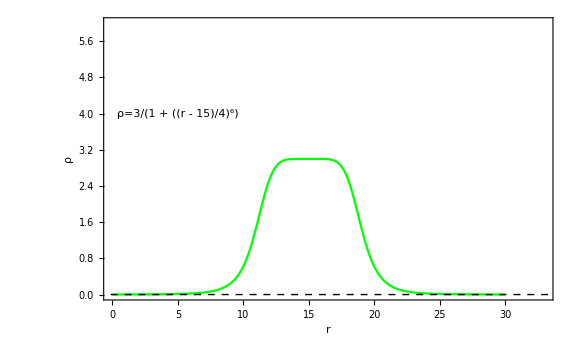

```mathematica
figmatshell=Show[plmat,Graphics[{Inset["ρ=3/(1 + SuperscriptBox[(FractionBox[r - 15, 4]), 6])",{5,4},BaseStyle->{Italic,Bold,Green,FontFamily->"Times",16}]}],PlotRange->{{-0.01,33},{0,6}},FrameLabel->{"r ","ρ"},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{Dashed,Darker[Black],Line[{{-1.2,0},{50,0}}]},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figmatshell.pdf",figmatshell,ImageResolution->1000];
```

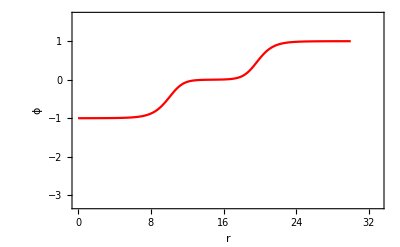

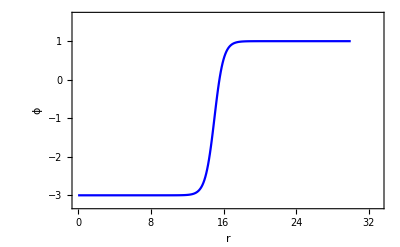

```mathematica
(* final  wall configuration *)
plsshellfin=ListPlot[tfsol,Joined->True,PlotRange->{{-0.01,33},{-3.25,1.65}},Axes->False,PlotStyle->Red,Frame->True,FrameLabel->{"r","ϕ"}]
(* initial  wall configuration *)
plsshellin=ListPlot[tstart,Joined->True,PlotRange->{{-0.01,33},{-3.25,1.65}},Axes->False,PlotStyle->Blue,Frame->True,FrameLabel->{"r","ϕ"}]
```

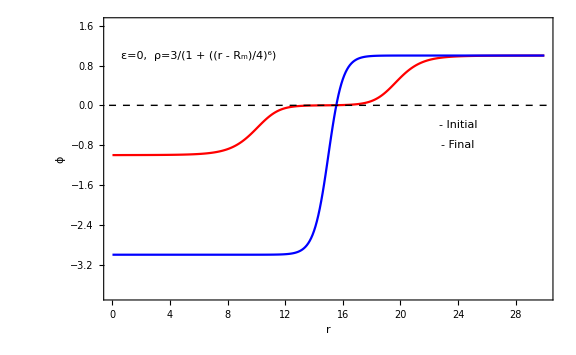

```mathematica
figsshell=Show[plsshellfin,plsshellin,Graphics[{Inset["ε=0,  ρ=3/(1 + SuperscriptBox[(FractionBox[r - SubscriptBox[R, m], 4]), 6])",{6,1.},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],Graphics[{Inset["- Initial",{24,-0.4},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",16}]}],Graphics[{Inset["- Final",{24,-0.8},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],PlotRange->{{-0.01,30},{-3.8,1.65}},FrameLabel->{"r ","ϕ"},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{Dashed,Darker[Black],Line[{{-1.2,0},{50,0}}]},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figsshell.pdf",figsshell,ImageResolution->1000];
```

## Figure 5 (right panel) - Figure 1 - II. Stable Spherical Asymmetron Walls - Shell-like matter density

2965.3

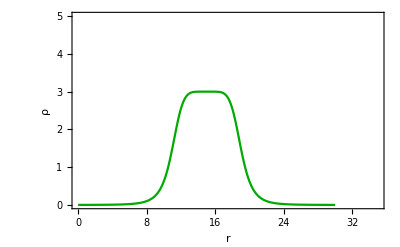

```mathematica
(* II.Stable Spherical Asymmetron Walls *)
Clear[r,fp,ee,dx,f,rmin,rmax,r0,ftab,sol1,rrb]
(* Energy Minimization (EM) method *)
r[i_]:=i dx;
fp[i_]:=(f[i]-f[i-1])/dx;
e=0.2; rt=4;n=6;rm=15;
rrb[r_]:=3/(1+((r-rm)/rt)^n);
ee[i_]:=r[i]^2fp[i]^2+r[i]^2(-(1-rrb[r[i]])f[i]^2+f[i]^4/2+1/2+2 e f[i]^3);
dx=0.05;
imax=600;
rmax=imax dx;
rmin=0;
rmax=r[imax];
f[0]=f[1];
phrmax=1;
phrmin=-3.3;
f[imax]=f[imax-1];
etot=dx  Sum[ee[i],{i,1,imax}];
r0=rmin+(rmax-rmin)/2;
(* Initial gues *)
ft[r_]:=((phrmax-phrmin)/2) Tanh[(r-rm)]+((phrmax+phrmin)/2);
ftab=Table[{f[i],ft[r[i]]},{i,1,imax-1}];
sol1=FindMinimum[etot,ftab,MaxIterations->1000000,AccuracyGoal->6];
etot /. sol1[[2]]
tfsol=Table[{i dx,f[i]/. sol1[[2]]},{i,0,imax}];
tstart=Table[{i dx,ft[r[i]]},{i,0,imax}];
(* Shell-like matter density *)
plmatas=Plot[rrb[r],{r,rmin,rmax},PlotRange->{{-0.01,35},{0,5}},PlotStyle->Darker[Green],Frame->True,FrameLabel->{"r","ρ"}]
```

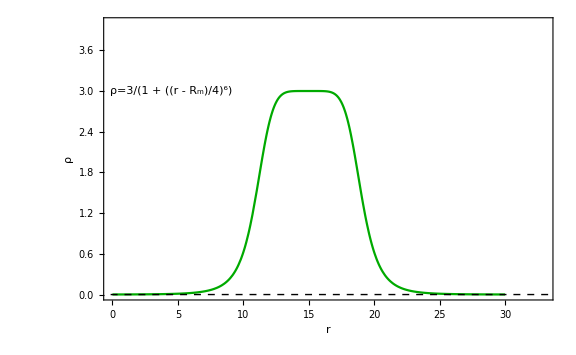

```mathematica
figmatshellas=Show[plmatas,Graphics[{Inset["ρ=3/(1 + SuperscriptBox[(FractionBox[r - SubscriptBox[R, m], 4]), 6])",{4.5,3},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],PlotRange->{{-0.01,33},{0,4}},FrameLabel->{"r ","ρ"},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{Dashed,Darker[Black],Line[{{-1.2,0},{50,0}}]},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figmatshellas.pdf",figmatshellas,ImageResolution->1000];
```

```mathematica
(* final  wall configuration *)
```

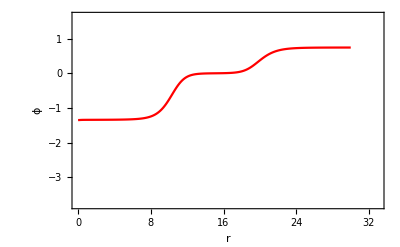

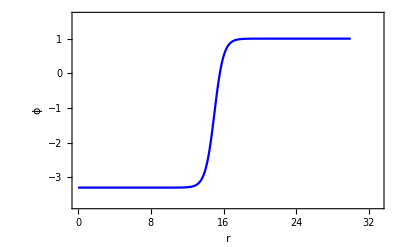

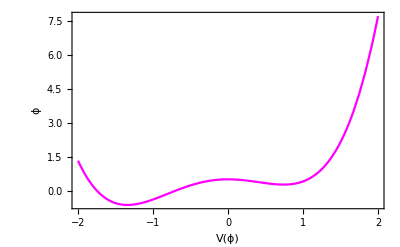

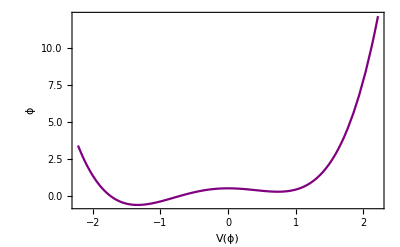

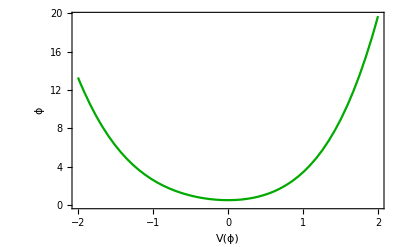

```mathematica
plasshellfin=ListPlot[tfsol,Joined->True,PlotRange->{{-0.01,33},{-3.8,1.65}},Axes->False,PlotStyle->Red,Frame->True,FrameLabel->{"r","ϕ"}]
(* initial  wall configuration *)
plasshellin=ListPlot[tstart,Joined->True,PlotRange->{{-0.01,33},{-3.8,1.65}},Axes->False,PlotStyle->Blue,Frame->True,FrameLabel->{"r","ϕ"}]
(* Asymmetron effective potential *)
plpotvac2=Plot[vv2/. rb->rrb[26],{phb,-2,2},Axes->False,PlotStyle->Magenta,PlotRange->All,Frame->True,FrameLabel->{"V(ϕ)","ϕ"}]
plpotvac1=Plot[vv2/. rb->rrb[5],{phb,-2.22,2.22},Axes->False,PlotStyle->Purple,PlotRange->All,Frame->True,FrameLabel->{"V(ϕ)","ϕ"}]
plpotmat=Plot[vv2/. rb->rrb[15],{phb,-2,2},Axes->False,PlotStyle->Darker[Green],Frame->True,FrameLabel->{"V(ϕ)","ϕ"}]
```

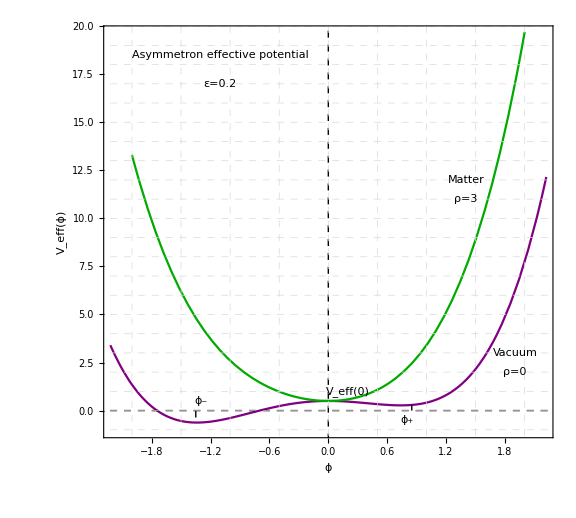

```mathematica
figpot=Show[plpotvac1,plpotmat,Graphics[{Inset["Asymmetron effective potential",{-1.1,18.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ε=0.2",{-1.1,17.},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ϕ_+",{0.8,-0.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ϕ_-",{-1.3,0.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["V_eff(0)",{0.2,1},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Vacuum",{1.9,3.},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset["ρ=0",{1.9,2.},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset["Matter",{1.4,12},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],Graphics[{Inset["ρ=3",{1.4,11},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],PlotRange->{{-2.2,2.2},{-1,19.6}},FrameLabel->{"ϕ","V_eff(ϕ)"},LabelStyle->{FontFamily->"Times",20},FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{{Dashed,Darker[Black],Line[{{-5,0},{5,0}}]},{Dashed,Darker[Black],Line[{{0,-3},{0,30}}]},{Dashed,Darker[Black],Line[{{-1.35,0},{-1.35,-0.5}}]},{Dashed,Darker[Black],Line[{{0.85,0},{0.85,0.3}}]}},GridLines->{{-2,-1.5,-1,-0.5,0,0.5,1,1.5,2},{-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}},GridLinesStyle->Directive[LightGray,Dashed],AspectRatio->0.9/1,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figpot.pdf",figpot,ImageResolution->1000];
```

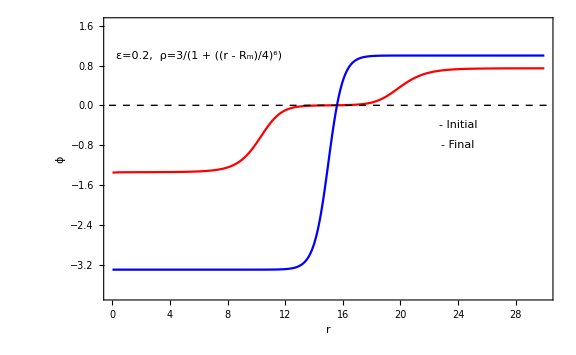

```mathematica
figasshell=Show[plasshellfin,plasshellin,Graphics[{Inset["ε=0.2,  ρ=3/(1 + SuperscriptBox[(FractionBox[r - SubscriptBox[R, m], 4]), 6])",{6,1.},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],Graphics[{Inset["- Initial",{24,-0.4},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",16}]}],Graphics[{Inset["- Final",{24,-0.8},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],PlotRange->{{-0.01,30},{-3.8,1.65}},FrameLabel->{"r ","ϕ"},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{Dashed,Darker[Black],Line[{{-1.2,0},{50,0}}]},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figasshell.pdf",figasshell,ImageResolution->1000];
```

## Figure 5

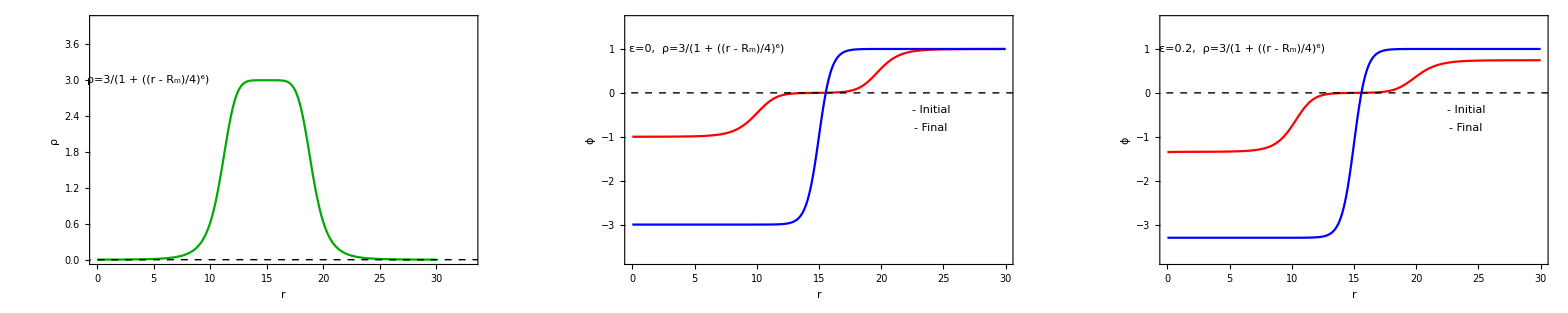

```mathematica
figshellall=GraphicsGrid[{{figmatshellas,figsshell,figasshell}},ImageSize->2500,AspectRatio->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"figshellall.pdf",figshellall,ImageResolution->1000];
```

## Figure 6 - Asymmetron effective potential

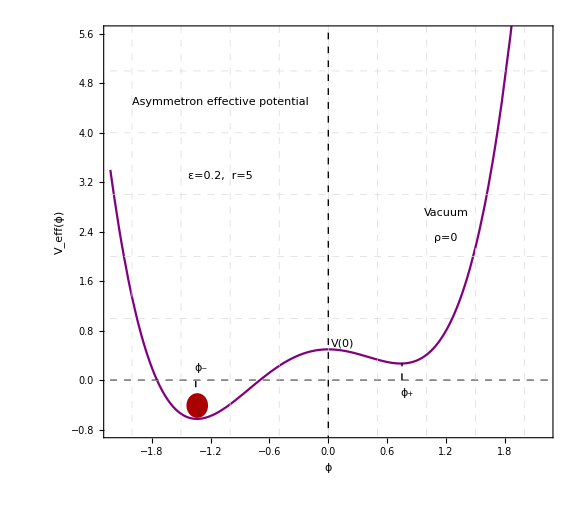

```mathematica
(* Snapshots of the potential and the corresponding field values *)

figpotr5=Show[plpotvac1,Graphics[{Inset["Asymmetron effective potential",{-1.1,4.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ε=0.2,  r=5",{-1.1,3.3},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ϕ_+",{0.8,-0.2},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ϕ_-",{-1.3,0.2},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["V(0)",{0.15,0.6},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Vacuum",{1.2,2.7},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset["ρ=0",{1.2,2.3},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],PlotRange->{{-2.2,2.2},{-0.8,5.6}},FrameLabel->{"ϕ","V_eff(ϕ)"},LabelStyle->{FontFamily->"Times",20},FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{{Dashed,Darker[Black],Line[{{-5,0},{5,0}}]},{Dashed,Darker[Black],Line[{{0,-1},{0,30}}]},{Dashed,Darker[Black],Line[{{-1.35,0},{-1.35,-0.5}}]},{Dashed,Darker[Black],Line[{{0.75,0},{0.75,0.28}}]},{Darker[Red],Disk[{-1.34,-0.4},{0.11,0.2}]}},GridLines->{{-2,-1.5,-1,-0.5,0,0.5,1,1.5,2},{-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}},GridLinesStyle->Directive[LightGray,Dashed],AspectRatio->0.9/1,ImageSize->Large]
```

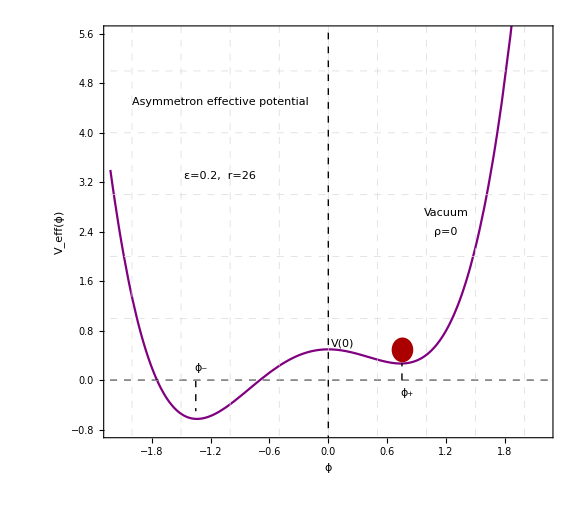

```mathematica
figpotr26=Show[plpotvac1,Graphics[{Inset["Asymmetron effective potential",{-1.1,4.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ε=0.2,  r=26",{-1.1,3.3},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ϕ_+",{0.8,-0.2},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ϕ_-",{-1.3,0.2},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["V(0)",{0.15,0.6},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Vacuum",{1.2,2.7},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset["ρ=0",{1.2,2.4},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],PlotRange->{{-2.2,2.2},{-0.8,5.6}},FrameLabel->{"ϕ","V_eff(ϕ)"},LabelStyle->{FontFamily->"Times",20},FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{{Dashed,Darker[Black],Line[{{-5,0},{5,0}}]},{Dashed,Darker[Black],Line[{{0,-1},{0,30}}]},{Dashed,Darker[Black],Line[{{-1.35,0},{-1.35,-0.5}}]},{Dashed,Darker[Black],Line[{{0.75,0},{0.75,0.28}}]},{Darker[Red],Disk[{0.75,0.5},{0.11,0.2}]}},GridLines->{{-2,-1.5,-1,-0.5,0,0.5,1,1.5,2},{-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}},GridLinesStyle->Directive[LightGray,Dashed],AspectRatio->0.9/1,ImageSize->Large]
```

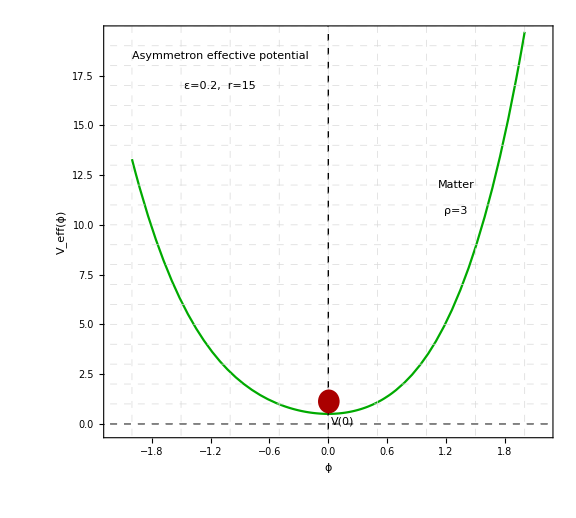

```mathematica
figpotr15=Show[plpotmat,Graphics[{Inset["Asymmetron effective potential",{-1.1,18.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["ε=0.2,  r=15",{-1.1,17.},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["V(0)",{0.15,0.1},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Matter",{1.3,12},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],Graphics[{Inset["ρ=3",{1.3,10.7},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],PlotRange->{{-2.2,2.2},{-0.3,19.6}},FrameLabel->{"ϕ","V_eff(ϕ)"},LabelStyle->{FontFamily->"Times",20},FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{{Dashed,Darker[Black],Line[{{-5,0},{5,0}}]},{Dashed,Darker[Black],Line[{{0,-1},{0,30}}]},{Darker[Red],Disk[{0,1.15},{0.11,0.6}]}},GridLines->{{-2,-1.5,-1,-0.5,0,0.5,1,1.5,2},{-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}},GridLinesStyle->Directive[LightGray,Dashed],AspectRatio->0.9/1,ImageSize->Large]
```

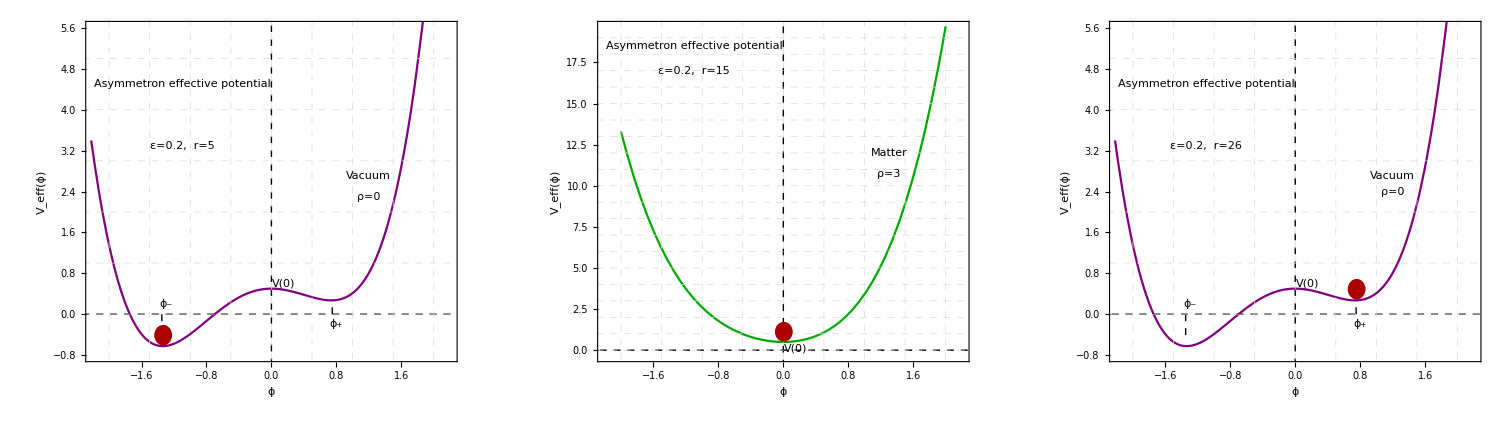

```mathematica
figr=GraphicsGrid[{{figpotr5,figpotr15,figpotr26}},ImageSize->1500,AspectRatio->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"figr.pdf",figr,ImageResolution->1000];
```

## Simulation of the evolution starting for minimum energy configuration (No evolution as expected and the wall remains static)

```mathematica
minensol= Interpolation[tfsol]
```

InterpolatingFunction[{{0., 30.}}, <>]

```mathematica
minensol[30]
```

0.743248

```mathematica
Vphi[t_,x_]=-(1-rrb[x])f[t,x]^2+f[t,x]^4/2+1/2+2 e  f[t,x]^3 ;
V[t_,x_]=Vphi[t,x];
dV[t_,x_]=D[Vphi[t,x],f[t,x]];
pde={D[f[t,r],t] ==g[t,r],r^2 D[g[t,r],t]== D[r^2  D[f[t,r],r],r]-0.5 dV[t,r] r^2};
(* parameters for initial conditions and boundary conditions *)
tmax=50; (* time for which evolution is run. *)
(* function to be used to specify initial conditions *)
rmin=0.01;
rmax=30;
bc={f[0,r]==minensol[r],
g[0,r]==0,Derivative[0,1][f][t,rmin]==0,g[t,rmin]==0,Derivative[0,1][f][t,rmax]==0,g[t,rmax]==0};
(* Now solve pde using NDSolve. *)
solution1=NDSolve[{pde,bc},{f,g},{r,rmin,rmax},{t,0,tmax},StartingStepSize->{Automatic,rmax/30},PrecisionGoal->2];
fsol1[t_,r_]:=f[t,r] /. solution1;
man2=Manipulate[Plot[fsol1[t,r],{r,rmin,rmax},FrameLabel->{"r ","ϕ"},Epilog->{Dashed,Darker[Black],Line[{{-1.2,0},{50,0}}]},LabelStyle->{FontFamily->"Times",20},Frame->True,Axes->None,FrameStyle->Directive[Black,Thick]],{t,0,tmax}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
man2=Manipulate[Plot3D[fsol1[t,Sqrt[x^2+y^2]],{x,-20,20},{y,-20,20},AxesLabel->{"x","y","ϕ"}],{t,0,tmax}]
```

## Figure 7 - Perturbed spherical asymmetron wall

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

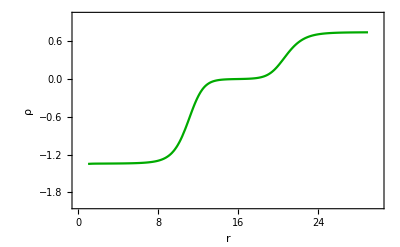

```mathematica
Vphi[t_,x_]=-(1-rrb[x])f[t,x]^2+f[t,x]^4/2+1/2+2 e  f[t,x]^3 ;
V[t_,x_]=Vphi[t,x];
dV[t_,x_]=D[Vphi[t,x],f[t,x]];
pde={D[f[t,r],t] ==g[t,r],r^2 D[g[t,r],t]== D[r^2  D[f[t,r],r],r]-0.5 dV[t,r] r^2};
(* parameters for initial conditions and boundary conditions *)
tmax=10; (* time for which evolution is run. *)
(* function to be used to specify initial conditions *)
rmin=1;
rmax=29;
dr=0.8;
bc={f[0,r]==minensol[r-dr],
g[0,r]==0,f[t,rmin]==minensol[rmin],g[t,rmin]==0,Derivative[0,1][f][t,rmax]==0,g[t,rmax]==0};
(* Solution of pde using NDSolve. *)
solution1=NDSolve[{pde,bc},{f,g},{r,rmin,rmax},{t,0,tmax},StartingStepSize->{Automatic,rmax/30},PrecisionGoal->2];
fsol1[t_,r_]:=f[t,r] /. solution1;
(* for time t=0 *)
plmant0=Plot[fsol1[0,r],{r,rmin,rmax},PlotRange->{{-0.01,30},{-2,1}},Axes->None,PlotStyle->Darker[Green],Frame->True,FrameLabel->{"r","ρ"}]
```

```mathematica
(* for time t=3*)
```

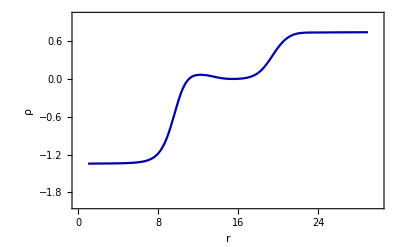

```mathematica
plmant3=Plot[fsol1[3,r],{r,rmin,rmax},PlotRange->{{-0.01,30},{-2,1}},Axes->None,PlotStyle->Darker[Blue],Frame->True,FrameLabel->{"r","ρ"}]
```

```mathematica
(* for time t=6 *)
```

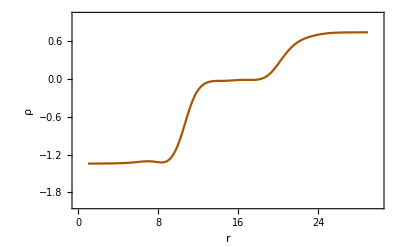

```mathematica
plmant6=Plot[fsol1[6,r],{r,rmin,rmax},PlotRange->{{-0.01,30},{-2,1}},Axes->None,PlotStyle->Darker[Orange],Frame->True,FrameLabel->{"r","ρ"}]
```

```mathematica
(* for time t=9 *)
```

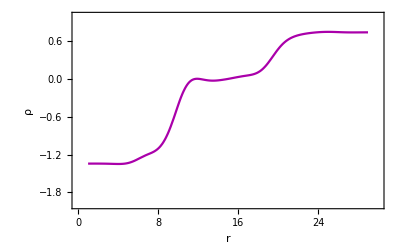

```mathematica
plmant9=Plot[fsol1[9,r],{r,rmin,rmax},PlotRange->{{-0.01,30},{-2,1}},Axes->None,PlotStyle->Darker[Magenta],Frame->True,FrameLabel->{"r","ρ"}]
```

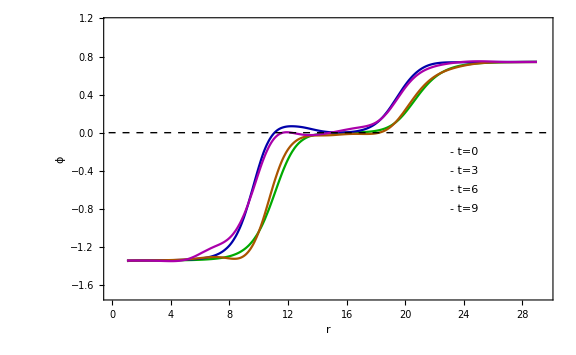

```mathematica
figpet=Show[plmant0,plmant3,plmant6,plmant9,Graphics[{Inset["- t=0",{24,-0.2},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],Graphics[{Inset["- t=3",{24,-0.4},BaseStyle->{Italic,Bold,Darker[Blue],FontFamily->"Times",16}]}],Graphics[{Inset["- t=6",{24,-0.6},BaseStyle->{Italic,Bold,Darker[Orange],FontFamily->"Times",16}]}],Graphics[{Inset["- t=9",{24,-0.8},BaseStyle->{Italic,Bold,Darker[Magenta],FontFamily->"Times",16}]}],PlotRange->{{-0.001,29.5},{-1.7,1.15}},FrameLabel->{"r ","ϕ"},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,Epilog->{Dashed,Darker[Black],Line[{{-1.2,0},{50,0}}]},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figpet.pdf",figpet,ImageResolution->1000];
```

```mathematica
man2=Manipulate[Plot[fsol1[t,r],{r,rmin,rmax}],{t,0,tmax}]
```

## Figure 8 - Mollweide projection view of 12 cluster locations in galactic coordinates

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
```

```mathematica
pls=BarLegend[{{"Rainbow","Reverse"},{0,8}},7,LegendMarkerSize->400,LabelStyle->Directive[Gray,FontSize->8,Italic],LegendLabel->"σ significance",LegendFunction->"Frame",LegendLayout->"Row"]
```

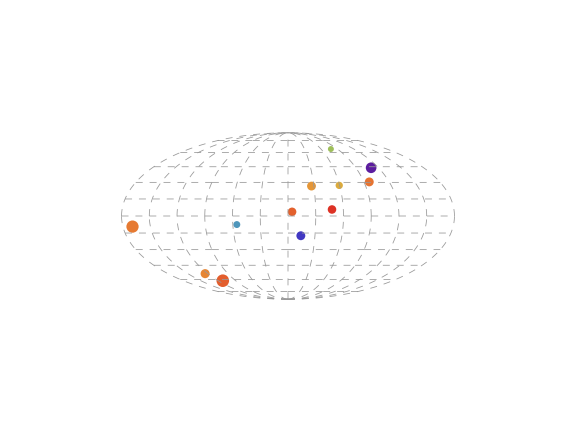

```mathematica
g1=GeoGraphics[{{ColorData[{"Rainbow","Reverse"},1.1/8],Disk[GeoPosition[{-9.301944,10.458750}],2 12.9/248]},{ColorData[{"Rainbow","Reverse"},5.47/8],Disk[GeoPosition[{-7.512778,124.352083}],2 9.8/332]},{ColorData[{"Rainbow","Reverse"},7.033/8],Disk[GeoPosition[{-17.400278,194.290417}],2 8.4/222]},{ColorData[{"Rainbow","Reverse"},1.52/8],Disk[GeoPosition[{26.595556,207.220833}],2 11/293]},{ColorData[{"Rainbow","Reverse"},0.2/8],Disk[GeoPosition[{5.720000,227.729167}],2 13.5/372]},{ColorData[{"Rainbow","Reverse"},2.009/8],Disk[GeoPosition[{27.226944,239.585833}],2 13.3/430]},{ColorData[{"Rainbow","Reverse"},3.437/8],Disk[GeoPosition[{64.092572,258.129364}],2 9.5/376]},{ColorData[{"Rainbow","Reverse"},7.65/8],Disk[GeoPosition[{43.958333,290.286667}],2 11.5/254]},{ColorData[{"Rainbow","Reverse"},1.27/8],Disk[GeoPosition[{-53.635278,55.724583}],2 10.5/273]},{ColorData[{"Rainbow","Reverse"},0.729/8],Disk[GeoPosition[{-61.443889,67.850417}],2 14.6/273]},{ColorData[{"Rainbow","Reverse"},1/8],Disk[GeoPosition[{30.441944,276.352917}],2 11.3/299]},{ColorData[{"Rainbow","Reverse"},0.77/8],Disk[GeoPosition[{3.662500,184.419167}],2 13.3/366]}},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->{Directive[Thickness[0.001],Dashed,GrayLevel[0.6]],Directive[Thickness[0.001],Dashed,GrayLevel[0.6]]},GeoBackground->None,PlotRange->{{-4,4},{-3,3}},GeoGridLines->{Range[-90,90,15],Range[0,360,30]},GeoProjection->"Mollweide",AxesStyle->Black,ImageSize->Large]
```

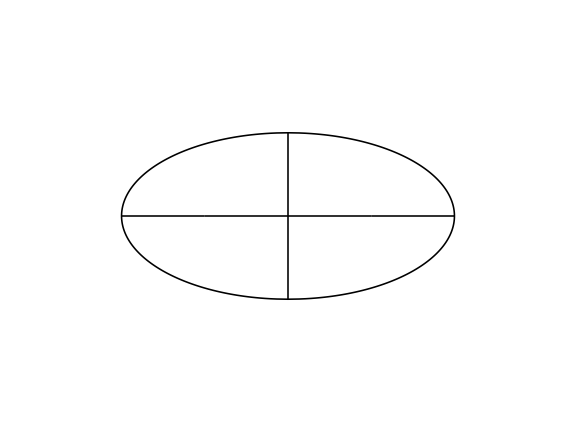

```mathematica
g2=GeoGraphics[GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->{Directive[Thickness[0.002],Black],Directive[Thickness[0.002],Black]},GeoBackground->None,PlotRange->{{-4,4},{-3,3}}, GeoGridLines->{Range[-90,90,90],Range[0,360,180]},Background->None,GeoProjection->"Mollweide",ImageSize->Large]
```

```mathematica
(*Mollweide-projection map*)
```

```mathematica
figclusterc=Show[Graphics[{Inset["0^0",{-2.98,0.02},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["60^0",{-1.87,0.07},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["120^0",{-1.05,0.07},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["180^0",{-0.18,0.07},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["240^0",{1.1,0.07},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["300^0",{1.87,0.07},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["360^0",{3.1,0.03},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["+30^0",{-2.76,0.6},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["+60^0",{-1.97,1.2},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["-30^0",{-2.82,-0.6},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["-60^0",{-2.1,-1.2},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["+90^0",{0,1.55},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset["-90^0",{0,-1.56},BaseStyle->{Black,FontFamily->"Times",12}]}],Graphics[{Inset[BarLegend[{{"Rainbow","Reverse"},{0,8}},15,LegendMarkerSize->300,LabelStyle->Directive[Gray,FontSize->8,Italic],LegendLabel->"σ significance",LegendFunction->"Frame",LegendLayout->"Row"],{0,-2.2}]}],Graphics[Rotate[{Darker[Green],Opacity[.2],Disk[{-0.3,-0.25},{0.2,0.8}]},80Degree]],Graphics[Rotate[{Darker[Green],Circle[{-0.3,-0.25},{0.2,0.8}]},80Degree]],Graphics[Rotate[{Darker[Green],Opacity[.2],Disk[{1.05,0.97},{0.2,0.6 }]},70Degree]],Graphics[Rotate[{Darker[Green],Circle[{1.05,0.97},{0.2,0.6 }]},70Degree]],Graphics[{Inset["R_point ∝ R_500/D",{-2.0,1.9},BaseStyle->{Bold,Black,FontFamily->"Courier",12}]}],
Epilog->{Inset[g1,Center,Center,Scaled[1]],Inset[g2,Center,Center,Scaled[1]]},PlotRange->{{-4,4},{-3.,3}},ImageSize->Large]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"figclusterc.pdf",figclusterc,ImageResolution->1000];
```